## Metricas del fluido perfecto e indice del politropo

```mathematica
ξ[r_]:=Log[(A-(B)*(r^2))^2];
μ[r_]:=-Log[1+(c)(r^2)((A)-3(r^2)(B))^(-2/3)];
Γ:=1+1/n
```

## Ecuación diferencial master para la obtención de la deformación del espacio f

```mathematica
DSolve[f'[r]/r+f[r]/r^2==-(Ka)^(Γ)(1/r^2-Exp[-μ[r]](1/r^2-μ'[r]/r)),f[r],r]
```

{{f[r]→(c Ka^(1+1/n) r^2)/((A-3 B r^2)^(2/3))+C[1]/r}}

```mathematica
f[r_]:=(c Ka^(1+1/n) r^2)/((A-3 B r^2)^(2/3))
```

## Ecuación diferencial para la obtención de la derivada de la deformación del tiempo

```mathematica
gprime[r_]:=(r/(Exp[-μ[r]]+f[r]))(κ Ka((Ka)^(Γ)/κ(1/r^2-Exp[-μ[r]](1/r^2-μ'[r]/r)))^(Γ) -f[r](1/r^2+ξ'[r]/r))
```

```mathematica
gprime[r]//FullSimplify
```

(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)))

```mathematica
gprime[r_]:=(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)));
```

## Cambio en la geometria del espacio-tiempo

### Derivada de ν, para el tiempo

```mathematica
νprime[r_]:=D[ξ[r],r]+gprime[r]
νprime[r]//FullSimplify
```

-(4 B r)/(A-B r^2)+(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)))

```mathematica
νprime[r_]:=-(4 B r)/(A-B r^2)+(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)));
```

### Cambio de λ, para el espacio

```mathematica
λ[r_]:=-Log[Exp[-μ[r]]+f[r]]
```

```mathematica
λ[r]//FullSimplify
```

-Log[1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))]

```mathematica
λ[r_]:=-Log[1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))];
```

## Ecuaciones de Einstein

### Densidad Efectiva

```mathematica
ρ[r_]:=1/(κ r^2)(1-ⅇ^(-λ[r])(1-r D[λ[r],r]));
ρ[r]//FullSimplify
```

-(c (1+Ka^(1+1/n)) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ)

```mathematica
ρ[r_]:=-(c (1+Ka^(1+1/n)) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ);
```

### Presión efectiva

```mathematica
Pr[r_]:=-1/(κ r^2)(1-ⅇ^(-λ[r])(1+r *νprime[r]));
Pr[r]//FullSimplify
```

1/((A-3 B r^2) (A-B r^2) κ)(-4 A B+12 B^2 r^2+c (A-5 B r^2) (A-3 B r^2)^(1/3)+Ka (A-3 B r^2) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)

```mathematica
Pr[r_]:=1/((A-3 B r^2) (A-B r^2) κ)(-4 A B+12 B^2 r^2+c (A-5 B r^2) (A-3 B r^2)^(1/3)+Ka (A-3 B r^2) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)
```

### Presión Tangencial efectiva

```mathematica
Pt[r_]:=Exp[-λ[r]]/(4κ)(2νprime'[r]+(νprime[r])^2-λ'[r]νprime[r]+(2(νprime[r]-λ'[r]))/r);
Pt[r]//Simplify
```

((1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))) (-2 c (1+Ka^(1+1/n)) n r^3 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n r^3 (A-3 B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)^2-2 n (A-3 B r^2) (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (-2 c (1+Ka^(1+1/n)) r (A-B r^2)^2+4 B r (A-3 B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))+r (A-3 B r^2) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))-2 r (8 B^2 n r^2 (A-3 B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+4 B n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+2 B c Ka^(1+1/n) r^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (n (A-5 B r^2) (A-3 B r^2)^2+2 n (A-5 B r^2) (A-3 B r^2) (A-B r^2)-5 n (A-3 B r^2)^2 (A-B r^2)+10 Ka (1+n) (A-B r^2)^3 (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1/n))-2 c (1+Ka^(1+1/n)) n r^2 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))))/(4 n r (A-3 B r^2)^2 (A-B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2 κ)

```mathematica
Pt[r_]:=((1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))) (-2 c (1+Ka^(1+1/n)) n r^3 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n r^3 (A-3 B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)^2-2 n (A-3 B r^2) (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (-2 c (1+Ka^(1+1/n)) r (A-B r^2)^2+4 B r (A-3 B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))+r (A-3 B r^2) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))-2 r (8 B^2 n r^2 (A-3 B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+4 B n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+2 B c Ka^(1+1/n) r^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (n (A-5 B r^2) (A-3 B r^2)^2+2 n (A-5 B r^2) (A-3 B r^2) (A-B r^2)-5 n (A-3 B r^2)^2 (A-B r^2)+10 Ka (1+n) (A-B r^2)^3 (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1/n))-2 c (1+Ka^(1+1/n)) n r^2 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))))/(4 n r (A-3 B r^2)^2 (A-B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2 κ)
```

## Resolución de la integral numérica de gprima, mediante MATLAB

```mathematica
gnume:=-0.003918
```

```mathematica
νnumer[r_]:=ξ[r]+gnume
```

## Aplicación de las condiciones de frontera

```mathematica
Solve[Exp[-λ[R]]==1-(2M)/R,c]
```

{{c→-(2 M (A-3 B R^2)^(2/3))/((1+Ka^(1+1/n)) R^3)}}

```mathematica
c:=-(2 M (A-3 B R^2)^(2/3))/((1+Ka^(1+1/n)) R^3)
```

```mathematica
NSolve[Exp[νnumer[R]]==1-(2M)/R,A]
```

{{A→1.02588×10^-8 (9.7477×10^7 B R^2-(9.76681×10^7 √(-2. M+R))/(√R))},{A→1.02588×10^-8 (9.7477×10^7 B R^2+(9.76681×10^7 √(-2. M+R))/(√R))}}

```mathematica
A:=1.025883123536302*^-8 (9.7476991*^7 B R^2-(9.766813559036595*^7 √(-2. M+R))/(√R))
```

### Damos las constantes que usamos en la integración

```mathematica
B=0.45;
Ka=0.7;
n=0.1;
κ=8*π;
R=1;
```

```mathematica
Clear[A,B,c,Ka,n,κ,R]
```

## Intercambio Energético

```mathematica
DEnergy[r_]:=gprime[r]/(2κ)×Exp[-μ[r]]/r(ξ'[r]+μ'[r])
DEnergy[r]/.{M->u R,r->x R}//FullSimplify
```

-((0.003052 x ((-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 x^2)+(0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3) (-2.40497×10^-29+5.35485×10^-29 √(1-2. u)+2.40497×10^-29 x^2) (((-0.9-1.00196 √(1-2. u))^(2/3) u (-1.34736+3. √(1-2. u)+2.2456 x^2))/((0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3) (-0.449119+1. √(1-2. u)+1.34736 x^2)))^11.) (1.98306 (-0.9-1.00196 √(1-2. u))^(2/3) u^2+(0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3) (0.203955-0.454121 √(1-2. u)-0.611864 x^2)+(-0.9-1.00196 √(1-2. u))^(2/3) u (-1.19153+0.890632 √(1-2. u)-1.648×10^-16 √(1-2. u) x^2+1. x^4)))/((0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3) (0.449119-1. √(1-2. u)-0.449119 x^2)^2 (-0.449119+1. √(1-2. u)+1.34736 x^2) (-2. (-0.9-1.00196 √(1-2. u))^(2/3) u x^2+1. (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3))))

```mathematica
DEnergy[x_]:=-((0.0030520018443734426 x ((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 x^2)+(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3) (-2.404967995975966*^-29+5.354853213433295*^-29 √(1-2. u)+2.404967995975966*^-29 x^2) (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-1.3473579387439492+3. √(1-2. u)+2.2455965645732485 x^2))/((0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3) (-0.44911931291464974+1. √(1-2. u)+1.3473579387439492 x^2)))^11.) (1.9830630822634054 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u^2+(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3) (0.20395465348600003-0.4541213161429097 √(1-2. u)-0.611863960458 x^2)+(-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-1.1915315411317036+0.8906319289725486 √(1-2. u)-1.6480001233527338*^-16 √(1-2. u) x^2+0.9999999999999999 x^4)))/((0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3) (0.44911931291464974-1. √(1-2. u)-0.44911931291464974 x^2)^2 (-0.44911931291464974+1. √(1-2. u)+1.3473579387439492 x^2) (-2. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2+1. (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3))))
```

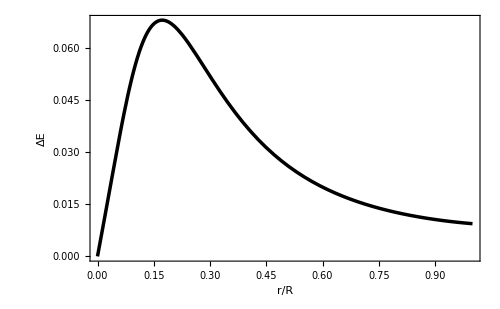

```mathematica
solu1:=Re[DEnergy[x]]/.{u->0.39}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ΔE"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
DEnergy[x]/.{x->√(x^2+y^2)}//FullSimplify
```

-((0.003052 √(x^2+y^2) ((-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 (x^2+y^2))+(0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-2.40497×10^-29+5.35485×10^-29 √(1-2. u)+2.40497×10^-29 (x^2+y^2)) (((-0.9-1.00196 √(1-2. u))^(2/3) u (-1.34736+3. √(1-2. u)+2.2456 (x^2+y^2)))/((0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.449119+1. √(1-2. u)+1.34736 (x^2+y^2))))^11.) (1.98306 (-0.9-1.00196 √(1-2. u))^(2/3) u^2+(0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.203955-0.454121 √(1-2. u)-0.611864 (x^2+y^2))+(-0.9-1.00196 √(1-2. u))^(2/3) u (-1.19153+0.890632 √(1-2. u)-1.648×10^-16 √(1-2. u) (x^2+y^2)+1. (x^2+y^2)^2)))/((0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.449119-1. √(1-2. u)-0.449119 (x^2+y^2))^2 (-0.449119+1. √(1-2. u)+1.34736 (x^2+y^2)) (-2. (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2)+1. (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3))))

```mathematica
dEnergy[x_,y_]:=-((0.0030520018443734426 √(x^2+y^2) ((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 (x^2+y^2))+(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-2.404967995975966*^-29+5.354853213433295*^-29 √(1-2. u)+2.404967995975966*^-29 (x^2+y^2)) (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-1.3473579387439492+3. √(1-2. u)+2.2455965645732485 (x^2+y^2)))/((0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.44911931291464974+1. √(1-2. u)+1.3473579387439492 (x^2+y^2))))^11.) (1.9830630822634054 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u^2+(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.20395465348600003-0.4541213161429097 √(1-2. u)-0.611863960458 (x^2+y^2))+(-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-1.1915315411317036+0.8906319289725486 √(1-2. u)-1.6480001233527338*^-16 √(1-2. u) (x^2+y^2)+0.9999999999999999 (x^2+y^2)^2)))/((0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.44911931291464974-1. √(1-2. u)-0.44911931291464974 (x^2+y^2))^2 (-0.44911931291464974+1. √(1-2. u)+1.3473579387439492 (x^2+y^2)) (-2. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2)+1. (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3))))
```

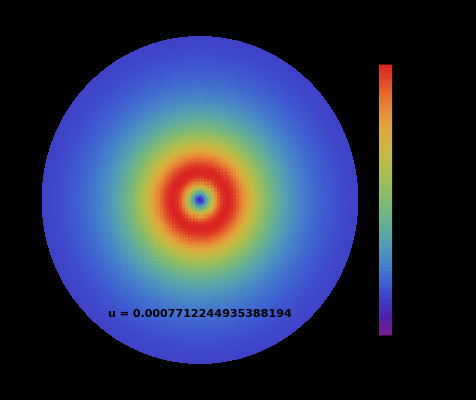

```mathematica
DensityPlot[Re[dEnergy[x,y]]/.{u->0.39},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.0007712244935388194",Large,Bold],{0,-0.7}],PlotPoints->100]
```

## Condiciones de aceptabilidad

### Sector material

```mathematica
Pr[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.0396331 (-0.81+1.80353 √(1-2. u)+2.43 x^2+2.08475×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 x^2))/((0.45-1.00196 √(1-2. u)-1.35 x^2)^(5/3)))^11. (-0.449119+1. √(1-2. u)+0.449119 x^2) (-0.449119+1. √(1-2. u)+1.34736 x^2)+(-0.9-1.00196 √(1-2. u))^(2/3) u (0.45-1.00196 √(1-2. u)-1.35 x^2)^(1/3) (-0.882549+1.96507 √(1-2. u)+4.41275 x^2)))/((-0.449119+1. √(1-2. u)+0.449119 x^2) (-0.449119+1. √(1-2. u)+1.34736 x^2))

```mathematica
Prg[x_]:=(0.03963314850071306 (-0.81+1.8035296561694103 √(1-2. u)+2.43 x^2+2.084749839244857*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 x^2))/(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(5/3))^11. (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 x^2) (-0.44911931291464974+1. √(1-2. u)+1.3473579387439492 x^2)+(-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(1/3) (-0.8825491202256668+1.9650660633990276 √(1-2. u)+4.412745601128334 x^2)))/((-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 x^2) (-0.44911931291464974+1. √(1-2. u)+1.3473579387439492 x^2))
```

```mathematica
Solve[Prg[1]==0,u]
```

$Aborted

```mathematica
Prg[1]/.u->0.40
```

0.00323216

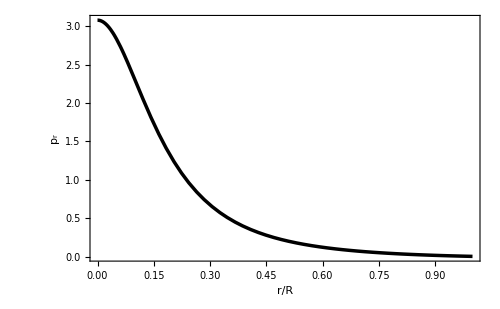

```mathematica
solu1:=Re[Prg[x]]/.{u->0.39}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","p_r"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Full]
```

```mathematica
Pt[r]/.{M-> u R, r->x R}//Simplify
```

(0.0246739 (1-(2. (-0.9-1.00196 √(1-2. u))^(2/3) u x^2)/((0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3))) (-1.30109 x^2 (0.449119-1. √(1-2. u)-1.34736 x^2)^2 (1. (-0.9-1.00196 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3))^2+1.44849 (0.449119-1. √(1-2. u)-1.34736 x^2)^2 (-0.449119+1. √(1-2. u)+0.449119 x^2) (1. (-0.9-1.00196 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3))^2+0.0698035 (-0.9-1.00196 √(1-2. u))^(2/3) u x^2 (-2. (-0.9-1.00196 √(1-2. u))^(2/3) u x^2+(0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3)) (-0.201179 (-0.449119+1. √(1-2. u))^3-0.81318 (0.449119-1. √(1-2. u))^2 x^2-0.933327 (-0.449119+1. √(1-2. u)) x^4-0.273375 x^6+0.402358 (-0.449119+1. √(1-2. u)) (0.449119-1. √(1-2. u)-1.34736 x^2)^2-5.92506×10^-28 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 x^2))/((0.45-1.00196 √(1-2. u)-1.35 x^2)^(5/3)))^10. (-0.449119+1. √(1-2. u)+0.449119 x^2)^3)+0.1 x^2 (0.45-1.00196 √(1-2. u)-1.35 x^2)^2 (3.6 (-0.9-1.00196 √(1-2. u))^(2/3) u x^2-1.8 (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3)-2.08067×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 x^2))/((0.45-1.00196 √(1-2. u)-1.35 x^2)^(5/3)))^11. (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3) (-0.449119+1. √(1-2. u)+0.449119 x^2)-0.0388558 (-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 x^2))^2-0.8 (-0.9-1.00196 √(1-2. u))^(2/3) u x^2 (0.45-1.00196 √(1-2. u)-1.35 x^2) (0.45-1.00196 √(1-2. u)-0.45 x^2)^2 (2.08067×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 x^2))/((0.45-1.00196 √(1-2. u)-1.35 x^2)^(5/3)))^11. (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3) (-0.449119+1. √(1-2. u)+0.449119 x^2)+0.0388558 (-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 x^2))-0.2 (0.45-1.00196 √(1-2. u)-1.35 x^2)^2 (0.45-1.00196 √(1-2. u)-0.45 x^2) (-2. (-0.9-1.00196 √(1-2. u))^(2/3) u x^2+(0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3)) (2.08067×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 x^2))/((0.45-1.00196 √(1-2. u)-1.35 x^2)^(5/3)))^11. (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3) (-0.449119+1. √(1-2. u)+0.449119 x^2)+0.0388558 (-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 x^2))+0.4 (-0.9-1.00196 √(1-2. u))^(2/3) u x^2 (0.45-1.00196 √(1-2. u)-1.35 x^2) (0.45-1.00196 √(1-2. u)-0.45 x^2)^2 (-3.6 (-0.9-1.00196 √(1-2. u))^(2/3) u x^2+1.8 (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3)+2.08067×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 x^2))/((0.45-1.00196 √(1-2. u)-1.35 x^2)^(5/3)))^11. (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3) (-0.449119+1. √(1-2. u)+0.449119 x^2)+0.0388558 (-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 x^2))-0.2 (0.45-1.00196 √(1-2. u)-1.35 x^2) (0.45-1.00196 √(1-2. u)-0.45 x^2) (-2. (-0.9-1.00196 √(1-2. u))^(2/3) u x^2+(0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3)) (4.0157 (-0.9-1.00196 √(1-2. u))^(2/3) u (0.449119-1. √(1-2. u)-0.449119 x^2)^2+3.60706 (-0.449119+1. √(1-2. u)+1.34736 x^2) (1. (-0.9-1.00196 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3))+(0.45-1.00196 √(1-2. u)-1.35 x^2) (2.08067×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 x^2))/((0.45-1.00196 √(1-2. u)-1.35 x^2)^(5/3)))^11. (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3) (-0.449119+1. √(1-2. u)+0.449119 x^2)+0.0388558 (-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 x^2)))))/((0.449119-1. √(1-2. u)-1.34736 x^2)^2 (0.449119-1. √(1-2. u)-0.449119 x^2)^2 (1. (-0.9-1.00196 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.00196 √(1-2. u)-1.35 x^2)^(2/3))^2)

```mathematica
Ptg[x_]:=(0.02467385601672154 (1-(2. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2)/((0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3))) (-1.3010876882730207 x^2 (0.44911931291464974-1. √(1-2. u)-1.3473579387439492 x^2)^2 (1. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3))^2+1.4484877969612924 (0.44911931291464974-1. √(1-2. u)-1.3473579387439492 x^2)^2 (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 x^2) (1. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3))^2+0.06980351909733327 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2 (-2. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2+(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3)) (-0.2011788606890684 (-0.44911931291464974+1. √(1-2. u))^3-0.8131798051706378 (0.44911931291464974-1. √(1-2. u))^2 x^2-0.9333265970676697 (-0.44911931291464974+1. √(1-2. u)) x^4-0.27337500000000003 x^6+0.40235772137813675 (-0.44911931291464974+1. √(1-2. u)) (0.44911931291464974-1. √(1-2. u)-1.3473579387439492 x^2)^2-5.92505797749639*^-28 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 x^2))/(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(5/3))^10. (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 x^2)^3)+0.1 x^2 (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^2 (3.6 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2-1.8 (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3)-2.0806698120012813*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 x^2))/(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(5/3))^11. (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3) (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 x^2)-0.038855776789206285 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 x^2))^2-0.8 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2 (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2) (0.45-1.0019609200941169 √(1-2. u)-0.45 x^2)^2 (2.0806698120012813*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 x^2))/(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(5/3))^11. (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3) (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 x^2)+0.038855776789206285 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 x^2))-0.2 (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^2 (0.45-1.0019609200941169 √(1-2. u)-0.45 x^2) (-2. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2+(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3)) (2.0806698120012813*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 x^2))/(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(5/3))^11. (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3) (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 x^2)+0.038855776789206285 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 x^2))+0.4 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2 (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2) (0.45-1.0019609200941169 √(1-2. u)-0.45 x^2)^2 (-3.6 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2+1.8 (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3)+2.0806698120012813*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 x^2))/(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(5/3))^11. (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3) (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 x^2)+0.038855776789206285 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 x^2))-0.2 (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2) (0.45-1.0019609200941169 √(1-2. u)-0.45 x^2) (-2. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2+(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3)) (4.015702741583397 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (0.44911931291464974-1. √(1-2. u)-0.44911931291464974 x^2)^2+3.6070593123388206 (-0.44911931291464974+1. √(1-2. u)+1.3473579387439492 x^2) (1. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3))+(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2) (2.0806698120012813*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 x^2))/(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(5/3))^11. (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3) (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 x^2)+0.038855776789206285 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 x^2)))))/((0.44911931291464974-1. √(1-2. u)-1.3473579387439492 x^2)^2 (0.44911931291464974-1. √(1-2. u)-0.44911931291464974 x^2)^2 (1. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u x^2-0.5 (0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(2/3))^2)
```

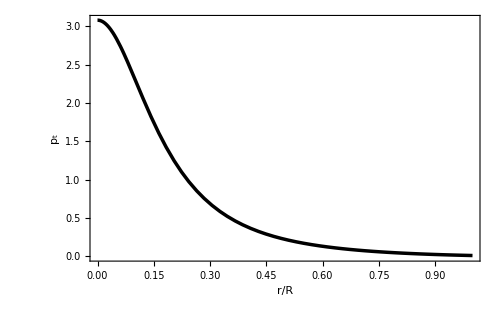

```mathematica
solu1:=Re[Ptg[x]]/.{u->0.39}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","p_t"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
ρ[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.0795775 (-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 x^2))/((0.45-1.00196 √(1-2. u)-1.35 x^2)^(5/3))

```mathematica
ρg[x_]:=(0.07957747154594767 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 x^2))/(0.45-1.0019609200941169 √(1-2. u)-1.35 x^2)^(5/3)
```

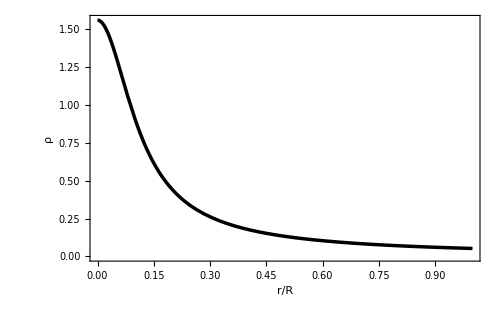

```mathematica
solu1:=Re[ρg[x]]/.{u->0.39}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Gráficas de componentes métricas del espacio-tiempo

```mathematica
Exp[νnumer[r]]/.{M->u R,r->x R}//FullSimplify
```

1. (0.00033079-1. √(1-2. u)-0.00033079 x^2)^2

```mathematica
metric1[x_]:=0.9999999999999998 (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 x^2)^2
```

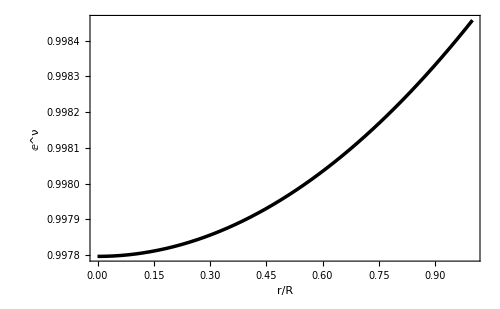

```mathematica
solu1:=Re[metric1[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ⅇ^ν"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Exp[-λ[r]]/.{M-> u R, r->x R}//FullSimplify
```

1-(2. (-0.9-1360.38 √(1-2. u))^(2/3) u x^2)/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3))

```mathematica
metric2[x_]:=1-(2. (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u x^2)/((0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3))
```

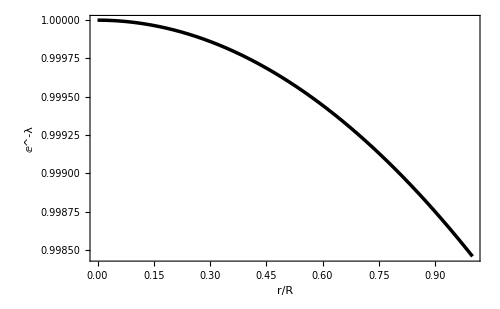

```mathematica
solu1:=Re[metric2[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ⅇ^-λ"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Condiciones de energía

#### Condición de energía dominante

```mathematica
dec1[x_]:=ρg[x]-Prg[x];
```

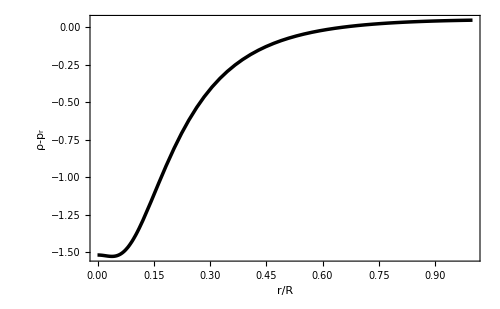

```mathematica
solu1:=Re[dec1[x]]/.{u->0.39}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-p_r"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
dec2[x_]:=ρg[x]-Ptg[x];
```

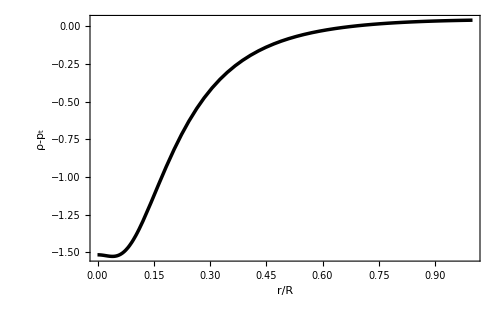

```mathematica
solu1:=Re[dec2[x]]/.{u->0.39}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-p_t"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

#### Condicion de energía fuerte

```mathematica
sec[x_]:=ρg[x]-Prg[x]-2*Ptg[x];
```

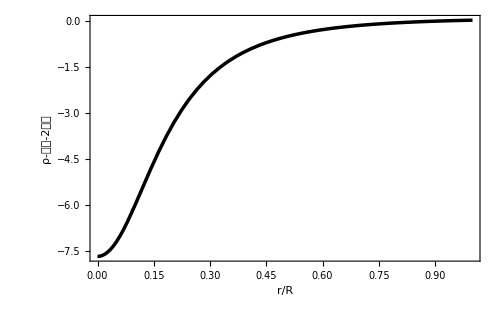

```mathematica
solu1:=Re[sec[x]]/.{u->0.39}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-𝓅𝓇-2𝓅𝓉"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Corrimiento al rojo

```mathematica
Z[r_]:=1/(√(ⅇ^(νnumer[r])))-1
```

```mathematica
Z[r]/.{M-> u R, r->x R}//FullSimplify
```

-1+1./(√((0.449119-1. √(1-2. u)-0.449119 x^2)^2))

```mathematica
Z[x_]:=-1+0.9999999999999998/(√((0.44911931291464974-1. √(1-2. u)-0.44911931291464974 x^2)^2))
```

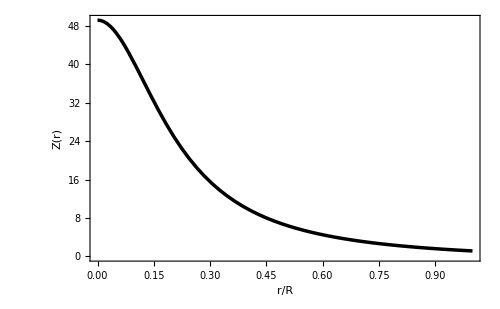

```mathematica
solu1:=Re[Z[x]]/.{u->0.39}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","Z(r)"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Condición de causalidad:?

#### Velocidad Radial?

```mathematica
vr[r_]:=D[Pr[r],r]/D[ρ[r],r]
```

```mathematica
vr[r]/.{M-> u R, r->x R}//FullSimplify
```

(3.64979×10^-14 (0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3) (1/π(0.45-1360.38 √(1-2. u)-1.35 x^2) (0.45-1360.38 √(1-2. u)-0.45 x^2) (4.86+((-0.9-1360.38 √(1-2. u))^(2/3) u (0.694459-2099.4 √(1-2. u)-3.4723 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(2/3))+7.71621 (-0.9-1360.38 √(1-2. u))^(2/3) u (0.45-1360.38 √(1-2. u)-1.35 x^2)^(1/3)+0.0742586 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.00033079+1. √(1-2. u)+0.00033079 x^2)-(0.247529 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.00033079-1. √(1-2. u)-0.00033079 x^2)^2)/(-0.00033079+1. √(1-2. u)+0.000551316 x^2)+0.0247529 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.00033079+1. √(1-2. u)+0.000992369 x^2))+0.286479 (0.45-1360.38 √(1-2. u)-1.35 x^2) (-0.81+2448.68 √(1-2. u)+2.43 x^2+37.4148 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.00033079+1. √(1-2. u)+0.00033079 x^2) (-0.00033079+1. √(1-2. u)+0.000992369 x^2)+(-0.9-1360.38 √(1-2. u))^(2/3) u (0.45-1360.38 √(1-2. u)-1.35 x^2)^(1/3) (-0.771621+2332.66 √(1-2. u)+3.85811 x^2))+0.859437 (0.45-1360.38 √(1-2. u)-0.45 x^2) (-0.81+2448.68 √(1-2. u)+2.43 x^2+37.4148 (((-0.9-1360.38 √(1-2. u))^(2/3) u (1.35-4081.14 √(1-2. u)-2.25 x^2))/((0.45-1360.38 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.00033079+1. √(1-2. u)+0.00033079 x^2) (-0.00033079+1. √(1-2. u)+0.000992369 x^2)+(-0.9-1360.38 √(1-2. u))^(2/3) u (0.45-1360.38 √(1-2. u)-1.35 x^2)^(1/3) (-0.771621+2332.66 √(1-2. u)+3.85811 x^2))))/((-0.9-1360.38 √(1-2. u))^(2/3) u (0.00033079-1. √(1-2. u)-0.00033079 x^2)^2 (1.7415×10^-7-0.000526468 √(1-2. u)-1.7415×10^-7 x^2))

```mathematica
vr[x_]:= (3.649794805791777*^-14 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3) (1/π(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2) (0.45-1360.3804781558129 √(1-2. u)-0.45 x^2) (4.86+((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.6944593291179939-2099.397587122892 √(1-2. u)-3.4722966455899695 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(2/3)+7.71621476797771 (-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(1/3)+0.07425859201003344 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2)-(0.24752864003344488 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 x^2)^2)/(-0.00033078981007580934+1. √(1-2. u)+0.0005513163501263489 x^2)+0.02475286400334448 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2))+0.2864788975654116 (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2) (-0.81+2448.6848606804633 √(1-2. u)+2.43 x^2+37.41479218732841 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2)+(-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(1/3) (-0.7716214767977709+2332.6639856921024 √(1-2. u)+3.858107383988855 x^2))+0.8594366926962349 (0.45-1360.3804781558129 √(1-2. u)-0.45 x^2) (-0.81+2448.6848606804633 √(1-2. u)+2.43 x^2+37.41479218732841 (((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (1.35-4081.1414344674386 √(1-2. u)-2.25 x^2))/(0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.00033078981007580934+1. √(1-2. u)+0.00033078981007580934 x^2) (-0.00033078981007580934+1. √(1-2. u)+0.000992369430227428 x^2)+(-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.45-1360.3804781558129 √(1-2. u)-1.35 x^2)^(1/3) (-0.7716214767977709+2332.6639856921024 √(1-2. u)+3.858107383988855 x^2))))/((-0.9000000000000001-1360.3804781558129 √(1-2. u))^(2/3) u (0.00033078981007580934-1. √(1-2. u)-0.00033078981007580934 x^2)^2 (1.7415036020815318*^-7-0.0005264683339799432 √(1-2. u)-1.7415036020815318*^-7 x^2))
```

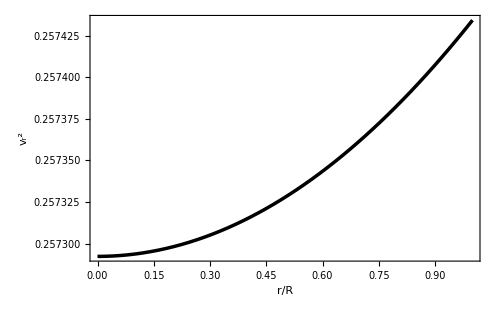

```mathematica
solu1:=vr[x]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_r^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

#### Velocidad Tangencial

```mathematica
vt[r_]:=D[Pt[r],r]/D[ρ[r],r]
vt[r]/.{M-> u R, r->x R}
```

(-((0.0397887 2 (2. 5 (-0.285286 (-1.35+0.0000501354 (8975.7-2.71341×10^7 √(1-2. u)))^(2/3) u (0.0000501354 (8975.7-2.71341×10^7 √(1-2. u))-2.25 x^2)-0.0000202173 (1)^3. 1 (0.0000501354 (8975.7-2.71341×10^7 √(1-1))-0.45 x^2)+1.8 (-2. (-1.35+0.0000501354 (8975.7-2.71341×10^7 √(1-1)))^(2/3) u x^2+(0.0000501354 (8975.7-1)-1.35 x^2)^(2/3)))+5))/(x (0.0000501354 (8975.7-2.71341×10^7 √(1-2. u))-1.35 x^2)^2 (0.0000501354 (8975.7-2.71341×10^7 √(1-2. u))-0.45 x^2)^2 (-2. (-1.35+0.0000501354 (8975.7-2.71341×10^7 1))^(2/3) u x^2+(0.0000501354 (8975.7-1)-1.35 1)^(2/3))^3))+1/(x 1^2 1 (1)^2)+1+1-1/1+(0.0198944 (1-(2. 1 u x^2)/(1)^(2/3)) (1))/(x (1-1)^2 (1)^2 (-2. 1 u x^2+1)^2))/((0.358099 (-1.35+0.0000501354 (8975.7-2.71341×10^7 √(1-2. u)))^(2/3) u x (0.000150406 (8975.7-2.71341×10^7 √(1-2. u))-2.25 x^2))/((0.0000501354 (8975.7-2.71341×10^7 √(1-2. u))-1.35 x^2)^(8/3))-(0.358099 (-1.35+0.0000501354 (8975.7-2.71341×10^7 √(1-2. u)))^(2/3) u x)/((0.0000501354 (8975.7-2.71341×10^7 √(1-2. u))-1.35 x^2)^(5/3)))
 |  |  |  |

```mathematica
vt[x_]:={{(-((0.039788735772973836 2 (2. 5 (-0.2852856071160648 (-1.35+0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u)))^(2/3) u (0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u))-2.25 x^2)-0.00002021727205555224 (1)^3. 1 (0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-1))-0.45 x^2)+1.8 (-2. (-1.35+0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-1)))^(2/3) u x^2+(0.0000501353654868144 (8975.7-1)-1.35 x^2)^(2/3)))+5))/(x (0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u))-1.35 x^2)^2 (0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u))-0.45 x^2)^2 (-2. (-1.35+0.0000501353654868144 (8975.7-2.7134149017295845*^7 1))^(2/3) u x^2+(0.0000501353654868144 (8975.7-1)-1.35 1)^(2/3))^3))+1/(x 1^2 1 (1)^2)+1+1-1/1+(0.019894367886486918 (1-(2. 1 u x^2)/(1)^(2/3)) (1))/(x (1-1)^2 (1)^2 (-2. 1 u x^2+1)^2))/((0.3580986219567646 (-1.35+0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u)))^(2/3) u x (0.00015040609646044319 (8975.7-2.7134149017295845*^7 √(1-2. u))-2.25 x^2))/(0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u))-1.35 x^2)^(8/3)-(0.3580986219567645 (-1.35+0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u)))^(2/3) u x)/((0.0000501353654868144 (8975.7-2.7134149017295845*^7 √(1-2. u))-1.35 x^2)^(5/3)))}, {{{, , , , }}}}
```

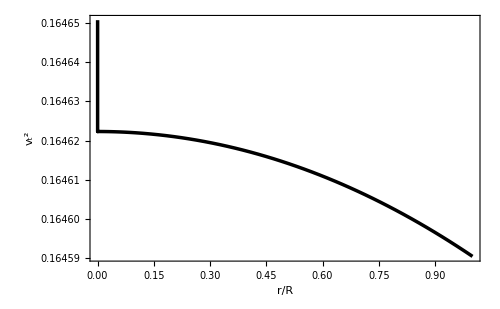

```mathematica
solu1:=Re[vt[x]]/.{u->0.0007712244935388194}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_t^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

## Anisotropía

```mathematica
Π[x_]:=Ptg[x]-Prg[x]
```

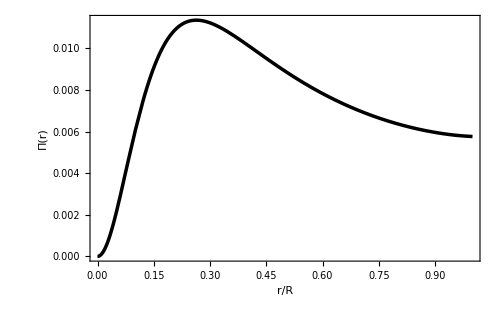

```mathematica
solu1:=Re[Π[x]]/.{u->0.39}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","Π(r)"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Π[x]/.{x->√(x^2+y^2)}//Simplify
```

-((0.0396331 (-0.81+1.80353 √(1-2. u)+2.43 (x^2+y^2)+2.08475×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^11. (-0.449119+1. √(1-2. u)+0.449119 (x^2+y^2)) (-0.449119+1. √(1-2. u)+1.34736 (x^2+y^2))+(-0.9-1.00196 √(1-2. u))^(2/3) u (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(1/3) (-0.882549+1.96507 √(1-2. u)+4.41275 (x^2+y^2))))/((-0.449119+1. √(1-2. u)+0.449119 (x^2+y^2)) (-0.449119+1. √(1-2. u)+1.34736 (x^2+y^2))))+(0.0246739 (1-(2. (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2))/((0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3))) (-1.30109 (x^2+y^2) (0.449119-1. √(1-2. u)-1.34736 (x^2+y^2))^2 (1. (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+1.44849 (0.449119-1. √(1-2. u)-1.34736 (x^2+y^2))^2 (-0.449119+1. √(1-2. u)+0.449119 (x^2+y^2)) (1. (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+0.0698035 (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2) (-2. (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (-0.201179 (-0.449119+1. √(1-2. u))^3-0.81318 (0.449119-1. √(1-2. u))^2 (x^2+y^2)-0.933327 (-0.449119+1. √(1-2. u)) (x^2+y^2)^2-0.273375 (x^2+y^2)^3+0.402358 (-0.449119+1. √(1-2. u)) (0.449119-1. √(1-2. u)-1.34736 (x^2+y^2))^2-5.92506×10^-28 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^10. (-0.449119+1. √(1-2. u)+0.449119 (x^2+y^2))^3)+0.1 (x^2+y^2) (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^2 (3.6 (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2)-1.8 (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3)-2.08067×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^11. (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.449119+1. √(1-2. u)+0.449119 (x^2+y^2))-0.0388558 (-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 (x^2+y^2)))^2-0.8 (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.00196 √(1-2. u)-0.45 (x^2+y^2))^2 (2.08067×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^11. (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.449119+1. √(1-2. u)+0.449119 (x^2+y^2))+0.0388558 (-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 (x^2+y^2)))-0.2 (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^2 (0.45-1.00196 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (2.08067×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^11. (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.449119+1. √(1-2. u)+0.449119 (x^2+y^2))+0.0388558 (-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 (x^2+y^2)))+0.4 (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.00196 √(1-2. u)-0.45 (x^2+y^2))^2 (-3.6 (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2)+1.8 (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3)+2.08067×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^11. (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.449119+1. √(1-2. u)+0.449119 (x^2+y^2))+0.0388558 (-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 (x^2+y^2)))-0.2 (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.00196 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (4.0157 (-0.9-1.00196 √(1-2. u))^(2/3) u (0.449119-1. √(1-2. u)-0.449119 (x^2+y^2))^2+3.60706 (-0.449119+1. √(1-2. u)+1.34736 (x^2+y^2)) (1. (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3))+(0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2)) (2.08067×10^-30 (((-0.9-1.00196 √(1-2. u))^(2/3) u (1.35-3.00588 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^11. (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.449119+1. √(1-2. u)+0.449119 (x^2+y^2))+0.0388558 (-0.9-1.00196 √(1-2. u))^(2/3) u (-0.449119+1. √(1-2. u)+2.2456 (x^2+y^2))))))/((0.449119-1. √(1-2. u)-1.34736 (x^2+y^2))^2 (0.449119-1. √(1-2. u)-0.449119 (x^2+y^2))^2 (1. (-0.9-1.00196 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.00196 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2)

```mathematica
Π[x_,y_]:=-((0.03963314850071306 (-0.81+1.8035296561694103 √(1-2. u)+2.43 (x^2+y^2)+2.084749839244857*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^11. (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 (x^2+y^2)) (-0.44911931291464974+1. √(1-2. u)+1.3473579387439492 (x^2+y^2))+(-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(1/3) (-0.8825491202256668+1.9650660633990276 √(1-2. u)+4.412745601128334 (x^2+y^2))))/((-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 (x^2+y^2)) (-0.44911931291464974+1. √(1-2. u)+1.3473579387439492 (x^2+y^2))))+(0.02467385601672154 (1-(2. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2))/((0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3))) (-1.3010876882730207 (x^2+y^2) (0.44911931291464974-1. √(1-2. u)-1.3473579387439492 (x^2+y^2))^2 (1. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+1.4484877969612924 (0.44911931291464974-1. √(1-2. u)-1.3473579387439492 (x^2+y^2))^2 (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 (x^2+y^2)) (1. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+0.06980351909733327 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2) (-2. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (-0.2011788606890684 (-0.44911931291464974+1. √(1-2. u))^3-0.8131798051706378 (0.44911931291464974-1. √(1-2. u))^2 (x^2+y^2)-0.9333265970676697 (-0.44911931291464974+1. √(1-2. u)) (x^2+y^2)^2-0.27337500000000003 (x^2+y^2)^3+0.40235772137813675 (-0.44911931291464974+1. √(1-2. u)) (0.44911931291464974-1. √(1-2. u)-1.3473579387439492 (x^2+y^2))^2-5.92505797749639*^-28 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^10. (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 (x^2+y^2))^3)+0.1 (x^2+y^2) (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^2 (3.6 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2)-1.8 (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3)-2.0806698120012813*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^11. (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 (x^2+y^2))-0.038855776789206285 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 (x^2+y^2)))^2-0.8 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.0019609200941169 √(1-2. u)-0.45 (x^2+y^2))^2 (2.0806698120012813*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^11. (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 (x^2+y^2))+0.038855776789206285 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 (x^2+y^2)))-0.2 (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^2 (0.45-1.0019609200941169 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (2.0806698120012813*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^11. (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 (x^2+y^2))+0.038855776789206285 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 (x^2+y^2)))+0.4 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.0019609200941169 √(1-2. u)-0.45 (x^2+y^2))^2 (-3.6 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2)+1.8 (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3)+2.0806698120012813*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^11. (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 (x^2+y^2))+0.038855776789206285 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 (x^2+y^2)))-0.2 (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2)) (0.45-1.0019609200941169 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (4.015702741583397 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (0.44911931291464974-1. √(1-2. u)-0.44911931291464974 (x^2+y^2))^2+3.6070593123388206 (-0.44911931291464974+1. √(1-2. u)+1.3473579387439492 (x^2+y^2)) (1. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3))+(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2)) (2.0806698120012813*^-30 (((-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (1.35-3.0058827602823506 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^11. (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.44911931291464974+1. √(1-2. u)+0.44911931291464974 (x^2+y^2))+0.038855776789206285 (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (-0.44911931291464974+1. √(1-2. u)+2.2455965645732485 (x^2+y^2))))))/((0.44911931291464974-1. √(1-2. u)-1.3473579387439492 (x^2+y^2))^2 (0.44911931291464974-1. √(1-2. u)-0.44911931291464974 (x^2+y^2))^2 (1. (-0.9000000000000001-1.0019609200941169 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-1.0019609200941169 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2)
```

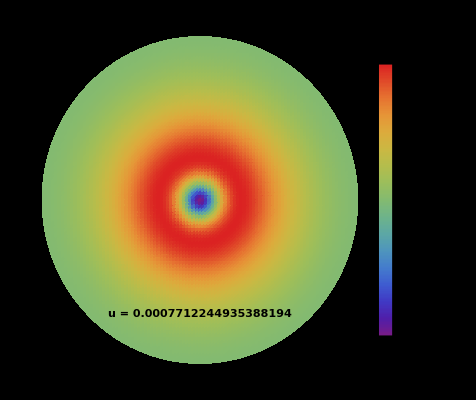

```mathematica
DensityPlot[Re[Π[x,y]]/.{u->0.39},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.0007712244935388194",Large,Bold],{0,-0.7}],PlotPoints->100]
```